```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
customNB[λ_,κ_]:= Module[{n=κ,p=κ/(κ+λ)},NegativeBinomialDistribution[n,p]]
```

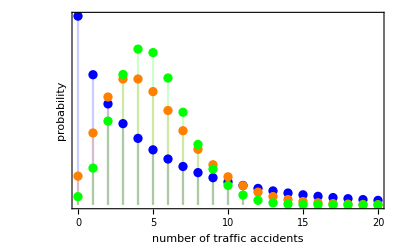

```mathematica
gSampling=DiscretePlot[{PDF[customNB[5,0.8],x],PDF[customNB[5,5],x],PDF[customNB[5,40],x]},{x,0,20},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"number of traffic accidents","probability"},FrameTicks->{True,False},BaseStyle->Medium,PlotStyle->{Blue,Orange,Green}]
```

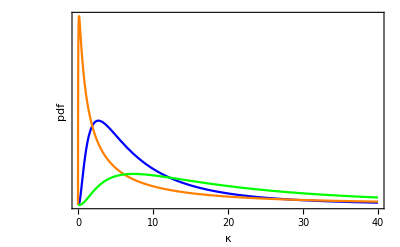

```mathematica
gPriors=Plot[{PDF[LogNormalDistribution[2,1],x],PDF[LogNormalDistribution[2,2],x],PDF[LogNormalDistribution[3,1],x]},{x,0,40},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"κ","pdf"},FrameTicks->{True,False},BaseStyle->Medium,PlotStyle->{Blue,Orange,Green}]
```

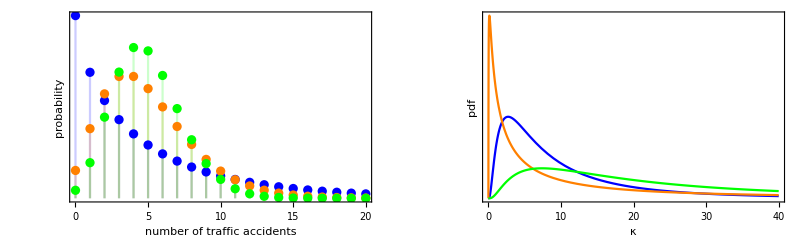

```mathematica
gFinal=Show[GraphicsRow[{gSampling,gPriors}],ImageSize->800]
```

```mathematica
Export["Distributions_lognormalPrior.pdf",gFinal]
```

Distributions_lognormalPrior.pdf